```mathematica
f[x_] := ArcTan[x]
g[x_] := 1
α=1;
h=0.01;
```

```mathematica
p[x_] := Evaluate[PDF[NormalDistribution[1/2,1/10],x]]
```

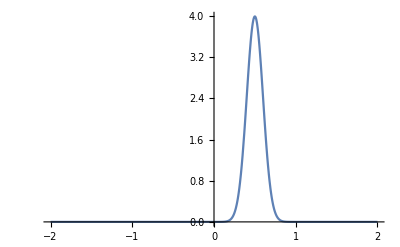

```mathematica
Plot[p[x],{x,-2,2},PlotRange->All]
```

```mathematica
ψ[s_]:=Evaluate[Integrate[Exp[I s x] p[x],{x,-Infinity,Infinity}]]
```

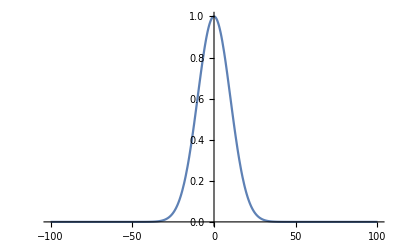

```mathematica
(* compute and plot this to figure out how big sgrid should be *)
Plot[Abs[ψ[s]],{s,-100,100},PlotRange->All]
```

```mathematica
(* create sgrid *)
bigs=100;
deltas=1;
sgrid=N[Table[i,{i,-bigs,bigs,deltas}]];
```

```mathematica
(* create mgrid *)
bigm=2;
deltax=1/100;
mgrid=N[Table[i,{i,-bigm,bigm,deltax}]];
```

```mathematica
psinew=Table[NIntegrate[Exp[I s y] Exp[h(I s f[y] - Abs[s g[y]]^α)]p[y],{y,-bigm,bigm}],{s,sgrid}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.532219}. NIntegrate obtained 4.8247×10^-18 - 5.55112×10^-17\ ⅈ and 2.15615×10^-16 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.507805}. NIntegrate obtained -3.55618×10^-17 + 9.1073×10^-18\ ⅈ and 1.45103×10^-16 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.509758}. NIntegrate obtained 1.56125×10^-17 - 2.8418×10^-18\ ⅈ and 2.17719×10^-16 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

```mathematica
ψnew=Interpolation[Transpose[{sgrid,psinew}],InterpolationOrder->1];
```

```mathematica
pnew=Table[NIntegrate[(1/(2 π)) Exp[-I u y]ψnew[u],{u,-bigs,bigs}],{y,mgrid}];
```

```mathematica
Total[Re[Table[y p[y],{y,mgrid}]]]*deltax
```

0.5

```mathematica
Total[mgrid*Re[pnew]]*deltax
```

0.488464

```mathematica
test[[102]]
```

{1.,0.862264+0.476226 ⅈ}

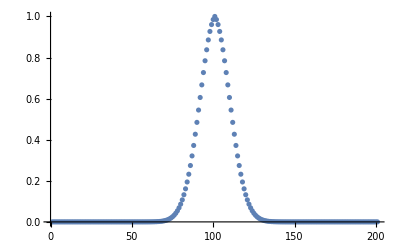

```mathematica
ListPlot[Abs[psinew],PlotRange->All]
```

```mathematica
Dimensions[pinit]
```

{401,201}

```mathematica
Length[sgrid]
Length[mgrid]
```

201

401